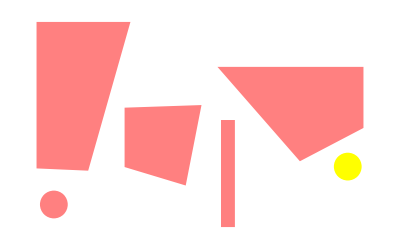

```mathematica
B1 = {{0.0,4.982},{0.0,1.426},{1.253,1.371},{2.278,4.982}};
B2 ={{2.136,2.90047},{2.136,1.459},{3.619,1.011},{4.002,2.964}};
B3 = {{4.475,0.002},{4.475,2.601},{4.812,2.601},{4.812,0.002}};
B4 ={{4.389,3.891},{6.389,1.6},{7.931,2.408},{7.931,3.891}};

St = {0.42,0.55} ;
Fin={7.52, 1.47};
fig1=Polygon[B1];
fig2=Polygon[B2];
fig3=Polygon[B3];
fig4=Polygon[B4];

col1 = Pink;
col2 = Pink;
col3 = Pink;
col4 = Pink;

g=Graphics[{{col1,fig1},{col2, fig2},{col3, fig3}, {col4, fig4}, {PointSize[0.05], Pink,Point[{0.42,0.55}]},{PointSize[0.05], Yellow,Point[{7.55,1.47}]}}]
```

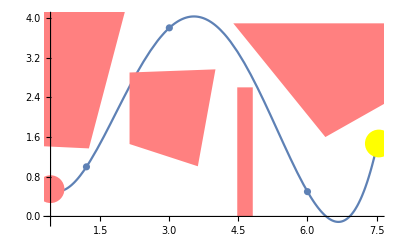

```mathematica
(*Решение задачи Ньютоном*)
(*Небольшшое количество точек*)
np=5;
XX={{St[[1]],1.2,3,6,Fin[[1]]},
 {St[[2]],1.0,3.8,0.5,Fin[[2]]}};XX=Transpose[XX] ;
RR =XX;
Do[R=Table[0,{j,np}];
Do[R[[i]]=(RR[[i,k]]-RR[[i-1,k]])/(RR[[i,1]]-RR[[i-k+1,1]]);,{i,k,np}];
RR=Transpose[Append[Transpose[RR],R]];,{k,2,np}]
RR//N // MatrixForm;
F=RR[[1,2]]+Sum[RR[[i+1,i+2]]Product[x-RR[[j,1]],{j,1,i}],{i,1,np-1}]//N;
FN=Simplify[F];
ris1=Plot[F,{x,St[[1]],Fin[[1]]}];
ris2=ListPlot[XX];
Show[ris1,ris2, g]
```

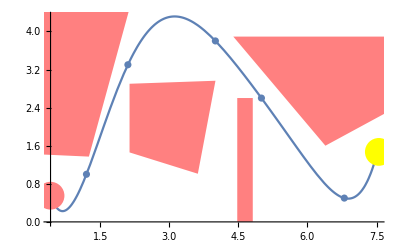

```mathematica
(*7 точек*)
np=7;
XX={{St[[1]],1.2,2.1,4,5,6.8,Fin[[1]]},
 {St[[2]],1.0,3.3,3.8,2.6,0.5,Fin[[2]]}};XX=Transpose[XX] ;
RR =XX;
Do[R=Table[0,{j,np}];
Do[R[[i]]=(RR[[i,k]]-RR[[i-1,k]])/(RR[[i,1]]-RR[[i-k+1,1]]);,{i,k,np}];
RR=Transpose[Append[Transpose[RR],R]];,{k,2,np}]
RR//N // MatrixForm;
F=RR[[1,2]]+Sum[RR[[i+1,i+2]]Product[x-RR[[j,1]],{j,1,i}],{i,1,np-1}]//N;
FN=Simplify[F];
ris1=Plot[F,{x,St[[1]],Fin[[1]]}];
ris2=ListPlot[XX];
Show[ris1,ris2, g]
```

36

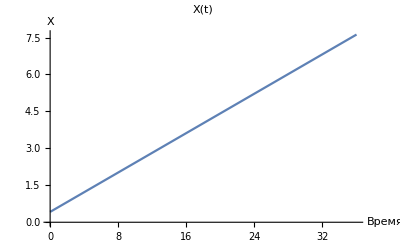

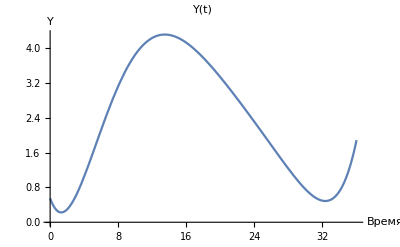

```mathematica
(*Пусть Vx(t)=const, тогда для метода Ньютона зависимости координат от времени будут:*)
Vx=0.2;
Xt =St[[1]]+Vx * t;
y=F/.(x->Xt);
time=36
Plot[Xt,{t,0,time},AxesLabel->{"Время", "X"}, PlotLabel->"X(t)"]
Plot[y,{t,0,time},AxesLabel->{"Время", "Y"}, PlotLabel->"Y(t)"]
```

14

10.4857-78.7844 x+248.519 x^2-411.576 x^3+405.055 x^4-253.268 x^5+105.078 x^6-29.6404 x^7+5.72508 x^8-0.748884 x^9+0.0640595 x^10-0.00332088 x^11+0.0000879744 x^12-7.09217×10^-7 x^13

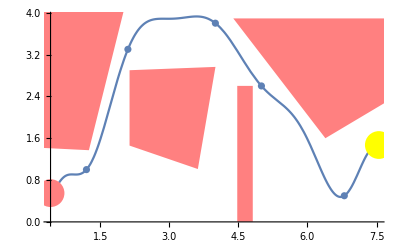

```mathematica
(*Эрмит*)
np=14
g1=Tan[0Degree];
g2=Tan[45Degree];
g3=Tan[65Degree];
g4=Tan[-35Degree];
g5=Tan[-45Degree];
g6=Tan[30Degree];
g7= Tan[20Degree];
XE={{St[[1]],St[[1]],1.2,1.2,2.1,2.1,4,       4,       5,       5,  6.8,6.8,Fin[[1]],Fin[[1]]},
 {    St[[2]], g1,             1.0,g2,3.3,g3,3.8,g4,2.6,g5,0.5,g6,Fin[[2]],g7}};XE=Transpose[XE];
RE=XE;
m1=(XE[[3,2]]-XE[[1,2]])/(XE[[3,1]]-XE[[1,1]]);
m2=(XE[[5,2]]-XE[[3,2]])/(XE[[5,1]]-XE[[3,1]]);
m3=(XE[[7,2]]-XE[[5,2]])/(XE[[7,1]]-XE[[5,1]]);
m4=(XE[[9,2]]-XE[[7,2]])/(XE[[9,1]]-XE[[7,1]]);
m5=(XE[[11,2]]-XE[[9,2]])/(XE[[11,1]]-XE[[9,1]]);
m6=(XE[[13,2]]-XE[[11,2]])/(XE[[13,1]]-XE[[11,1]]);
RE=Transpose[Append[Transpose[RE],{0,XE[[2,2]],m1,XE[[4,2]],m2,XE[[6,2]],m3,XE[[8,2]],m4,XE[[10,2]],m5,XE[[12,2]],m6,XE[[14,2]]}]];
Do[Rs=Table[0,{j,np}];
Do[Rs[[i]]=(RE[[i,k]]-RE[[i-1,k]])/(RE[[i,1]]-RE[[i-k+1,1]]);,{i,k,np}];
RE=Transpose[Append[Transpose[RE],Rs]];,{k,3,np}]
RE//N//MatrixForm;
FE=RE[[1,2]]+Sum[RE[[i+1,i+2]]Product[x-RE[[j,1]],{j,1,i}],{i,1,np-1}]//N;
FES=Simplify[FE]

ris1=Plot[FE,{x,St[[1]],Fin[[1]]}];
ris2=ListPlot[XX];
Show[ris1,ris2,g]
```

36

-Graphics-

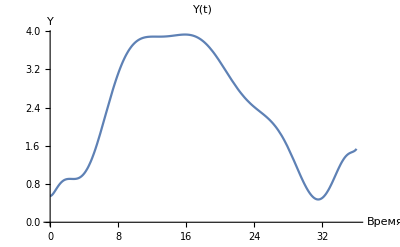

```mathematica
(*Эрмит, зависимости координат от времени:*)
Vx=0.2;
Xt =St[[1]]+Vx * t;
y=FE/.(x->Xt);
time=36
Plot[Xt,{t,0,time},AxesLabel->{"Время", "X"}, PlotLabel->"X(t)"]
Plot[y,{t,0,time},AxesLabel->{"Время", "Y"}, PlotLabel->"Y(t)"]
```